# Homework #1

## Derek Prince APPM 2450 - 002, Fall 2015 Due 28 August, 2015

```mathematica
Clear["Global`*"];
```

## Problem 1

For the formatting, I just followed Cell to Row to Grid and used the examples until I was happy with my formatting.
As far as matching answers, this is exactly what the notes cover from day 1. I’m not sure what else to say, the explanations were given in the problem.

```mathematica
Text[Grid[{{"1 ->", "(a)"},{"2 ->", "(b)"}, {"3 ->", "(c)"}, {"4 ->", "(d)"}}]]
```

1 -> | (a)
2 -> | (b)
3 -> | (c)
4 -> | (d)

## Problem 2

```mathematica
To check for continuity, evaluating (sin(θ))/θ as a limit as θ approaches 0 to check if it evaluates to 1 will do. The point 0, and thus where θ approaches 0 is the main area of concern, as (sin(θ))/θ is undefined at θ = 0. This is the only point in question because the function exists at every other value of θ, as -1 ≤ sin(θ) ≤ 1 and θ only takes on real values.
```

```mathematica
f[θ_] = Sin[θ] / θ (* Set function *)
Limit[f[θ],θ->0] (* Limit as θ approaces 0 *)
```

Sin[θ]/θ

1

Since (sin(θ))/θ evaluates to 1 when θ approaches 0, and f(θ) is equal to 1 when θ = 0, f(θ) must be continuous.

Plot 1: Red line from -5π to 5π, and -0.3 to 1 with a Plot label of f(θ) and a filling to the axis.
Plot 2: Thick blue line, same scope as Plot 1, Auto axis label.
Plot 3: Dot-dash green line, same scope as previous plots, manual labels of θ and the function for (x,y).

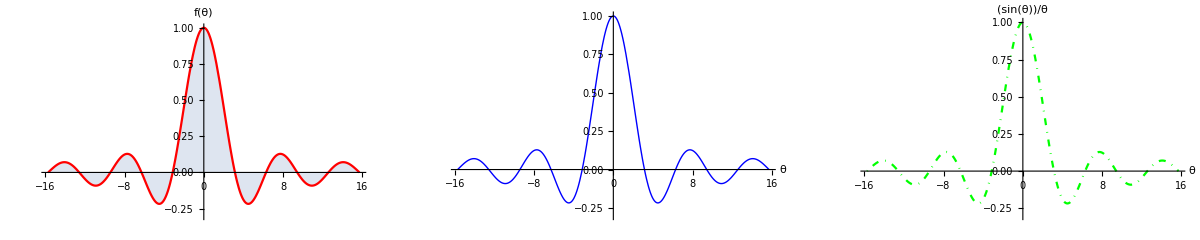

```mathematica
GraphicsRow[{
Plot[Style[f[θ], Red],{θ, -5 π, 5 π}, PlotRange->{-0.3, 1}, PlotLabel-> "f(θ)", Filling->Axis], 
Plot[Style[f[θ], Blue, Thick],{θ, -5 π, 5 π}, PlotRange->{-0.3, 1}, AxesLabel -> Automatic], 
Plot[Style[f[θ], Green, DotDashed],{θ, -5 π, 5 π}, PlotRange->{-0.3, 1}, AxesLabel-> {θ, f[θ]}]
}, ImageSize->Full, Frame->All] 
(* The row looks normal under wide-screen conditions due to scaling from `ImageSize -> Full` *)
```

## Problem 3